```mathematica
Quit[];
```

# A tutorial to use QuantumManyBody package

This notebook has to be considered as a tutorial, which will explain how to use the QuantumManyBody package to perform numerical computations. The package can be useful to simulate quantum mechanical systems in 1 dimension; such as spin chain models (having, say, L, spin sites) and the so-called SYK model, which is a strongly interacting model of N Majorana fermions, which will be included and discussed at length in a dedicated section.

First of all, let us load the package:

```mathematica
Needs["QuantumManyBody`"]
```

and we will focus first on showing functionalities which can be used to generate spin chain Hamiltonians. For simplicity, we will consider chains having 10 sites, which are then associated to Hilbert spaces of dimension 2^10

```mathematica
latticeSize = 10;
length = 2^latticeSize;
```

## Creating spin chain Hamiltonians using SpinChainHamiltonian

The first function we want to address is the function SpinChainHamiltonian[listCouplings , listCoefficients]. Most of the Hamiltonians used in condensed matter are built out of lattices (defined on graphs) in which the spin variables (that here we call σ_i^a, with i being the site on the graph and a = x, y, z being the orientation of the spin along the 3 axes) interact through scalar products when they are connected by an edge of the underlying graph.

We will see through some examples, which kind of Hamiltonians can be generated and how.

## The Heisenberg model example

To start with, we will consider probably the simplest yet non-trivial example of Hamiltonian: the Heisenberg chain with periodic boundary conditions. In this model, the spins variables are placed on a necklace like graph;  only the nearest neighbors sites interact among each other, with a constant coupling.
In formulas, the Hamiltonian reads

H_Heis = ∑_(i j) ∑_(a=1)^3 σ_i^a · σ_j^a

where the notation ( i j)  denotes the nearest neighbors pairs

To build this hamiltonian, we first create a list, which contains all the nearest neighbors pairs <i j>

```mathematica
listCouplings = Partition[Range @ latticeSize , 2 , 1 , 1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}}

Notice that we are assuming periodic boundary conditions, given the presence of the coupling {10 , 1}. We can similarly consider the case with open boundary conditions

```mathematica
listCouplingsOpen = Partition[Range @ latticeSize , 2 , 1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

In which we see that the last coupling {10 , 1}, which was ``closing” the necklace, is now removed. From the formula for the Hamiltonian H_Heis, we see that, for each non trivial coupling <i j> the three spin operators are coupled  isotropically with strength one. From this we learn that the list of the coefficients, listCoefficients, is simply given by

```mathematica
listCoefficients = ({1 , 1 , 1} &) /@ Range @ Length @ listCouplings
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

Given these two ingredients, we are ready to build our Hamiltonian, using SpinChainHamiltonian

```mathematica
{hamiltonianHeisenbergDecomposed , hamiltonianHeisenberg} = SpinChainHamiltonian[listCouplings , listCoefficients]
```

{{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}},SparseArray[…]}

As we see, the output is given by two lists: the first list, here called hamiltonianHeisenbergDecomposed, contains all the single terms σ_i^a · σ_j^a, organized as a nested list, in which, for each non-vanishing choice of the site indices i and j, the three individual terms with a = x, y, z are separately considered. This list is relevant because each element has the property of being proportional to a unitary operator (in this particular example they are effectively unitary). Hence, hamiltonianHeisenbergDecomposed can be useful when we deal with algorithms which make use of a Trotterization of the Hamiltonian (we will see an example  in a later section).
The second list, here called hamiltonianHeisenberg denotes instead the full Heisenberg Hamiltonian, H_Heis.

Notice that all the resulting matrices are given as SparseArray. This is convenient, since the Heisenberg Hamiltonian, as well as most of the Hamiltonians used in condensed matter physics, are very sparse:

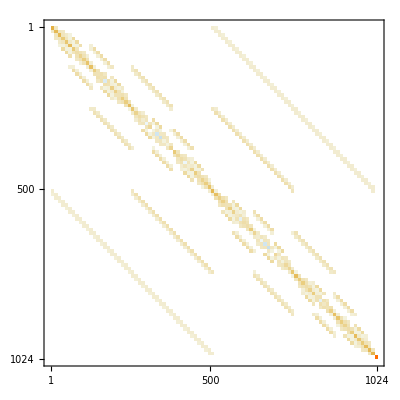

```mathematica
hamiltonianHeisenberg // MatrixPlot
```

## A more interesting example

Let us now turn to a more interesting example: we will consider an Hamiltonian having both single site terms as well as nearest neighbors and next-to-nearest neighbors couplings. It reads (we are assuming here open boundary conditions)

H = h ∑_(i=1)^L σ_i^x - ∑_(i=1)^(L - 1) J_i σ_i^z·(σ_(i+1))^z+ J_2∑_(i=1)^(L - 2) σ_i^z·(σ_(i + 2))^z ≡ H_0 + H_1 + H_2

where the constant h is set to h = 0.6,  J_2 is set to J_2 = 0.3 and the random variables J_i are taken to be J_i = 1 + δJ_i with the variables δJ_i extracted randomly from a uniform distribution with support [-1 , 1];

Let us start by constructing the three terms separately, starting from the easiest, H_0

```mathematica
h = 0.6;
```

```mathematica
couplingsH0 = {Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize}
```

{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}},{{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0}}}

Let us now move to H_1

```mathematica
couplingsH1 = {Partition[Range @ latticeSize ,2 , 1] , ({0 , 0 , - (1 + RandomReal[{-1 , 1}])} &) /@ Range @ Length @ Partition[Range @ latticeSize ,2 , 1]}
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}},{{0,0,-0.957698},{0,0,-1.84172},{0,0,-1.44022},{0,0,-1.38398},{0,0,-1.76864},{0,0,-1.34646},{0,0,-1.24338},{0,0,-0.999613},{0,0,-1.95009}}}

and finally we do the H_2 term

```mathematica
j2 = 0.3; 
couplingsH2 = {({# , # + 2} &)/@ Range[latticeSize - 2] , ({0 , 0 , j2} &) /@ Range @ Length @ Range[latticeSize - 2]}
```

{{{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,10}},{{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3}}}

Now that we have all the terms, we can simply join them

```mathematica
couplingsFullH = Join @@@ Transpose @ {couplingsH0 , couplingsH1 , couplingsH2}
```

{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,10}},{{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0,0,-0.957698},{0,0,-1.84172},{0,0,-1.44022},{0,0,-1.38398},{0,0,-1.76864},{0,0,-1.34646},{0,0,-1.24338},{0,0,-0.999613},{0,0,-1.95009},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3}}}

and get the final Hamiltonian (as well as its decomposition in terms of unitaries)

```mathematica
{hamiltonianDecomposed , hamiltonianFull} = SpinChainHamiltonian @@ couplingsFullH
```

{{{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]}},SparseArray[…]}

let us check that all the decomposed terms are proportional to unitary matrices: as a first step let us check if the product of the elements with their conjugate transpose give diagonal matrices

```mathematica
Map[(DiagonalMatrixQ[ConjugateTranspose @ # . #]  &), hamiltonianDecomposed , {2}]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

the answer is positive, so it just remains to check that the diagonal elements are all equals to each other. To do this, we tally all the elements of the diagonals and check if the resulting list has length equal to one

```mathematica
Map[(Length @ Tally @ Diagonal[ConjugateTranspose @ # . #]  &), hamiltonianDecomposed , {2}]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

We can also visualize the level of sparsity of the full hamiltonian

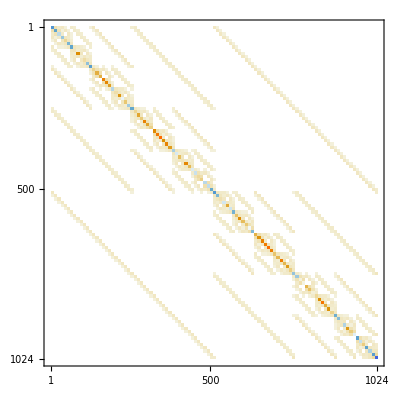

```mathematica
hamiltonianFull // MatrixPlot
```

## Quantum imaginary time evolution using QITE

```mathematica
groundStateHeisenberg = Chop[FindGroundState @ hamiltonian, 10^-8];
groundEnergyHeisenberg = EnergyStored[groundStateHeisenberg , hamiltonian]
```

-18.0618

```mathematica
β = 3.;
Δt = 0.1;
```

```mathematica
initialState = SparseArray[((Position[#,Min[#]]&) @ Normal @ Diagonal @ hamiltonian)[[1 ]] -> 1. , {2^latticeSize} , 0];
```

```mathematica
dD = 1;
```

```mathematica
evolvedKetHeisenberg = QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , dD];
```

```mathematica
energyHeisenberg = ({#1 ,1/groundEnergyHeisenberg * Conjugate @ #2 . hamiltonian . #2} &)@@@ evolvedKetHeisenberg ;
```

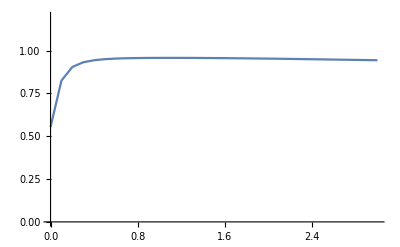

```mathematica
ListPlot[energyHeisenberg , Joined->True , PlotRange->{All , {0. , 1.2}}]
```